Read me

This notebook can be used to reproduce the results shown in Fig. 3 of “Online quantum time series processing with random oscillator networks” (https://arxiv.org/abs/2108.00698) in the manner described in the preprint. It requires a working installation of a recent version of Wolfram Mathematica. It has been tested in Wolfram Mathematica 11.2 for Microsoft Windows (64-bit). 

To use it, evaluate Sections 1 and  2.1 first. The parameter “realizations” controls how many samples are used to generate the ensemble averages and is by default set to 10. In “Online quantum time series processing with random oscillator networks” a value of 100 has been used, but notice that this might take a while to finish.

Then you can proceed with 2.2,  2.3 and 2.4 in that order. Inside these subsections cells should also in general be evaluated in order, i.e. plots can be made only after data has been generated and so on. All need to be evaluated before 2.5 which simply combines the results into a single figure. 

The author of this notebook is Johannes Nokkala. Any inquiries about its contents can be sent to jsinok@utu.fi

Summary of the license
This work is licensed under CC BY 4.0. You are free to share and adapt the material as long as it remains under the same license  and you give appropriate credit. For the full legal text see LICENSE in the main repository.

1 Preliminaries

We will clear all values, definitions, attributes, messages, and defaults associated with symbols in the global context. This is to prevent problems with pre-existing symbol definitions.

```mathematica
ClearAll["Global`*"];
```

We will set the history length to 0 to keep memory consumption in check. That is to say none of the previous input and output lines are saved by default for later use, only the ones we explicitly keep.

```mathematica
$HistoryLength=0;
```

Parallelization is used to speed up certain parts of the computations. We launch the maximum number of them now.

```mathematica
If[$ProcessorCount-$KernelCount>0,LaunchKernels[$ProcessorCount-$KernelCount]]
```

## User-defined functions

### Auxiliary

#### Permutations

```mathematica
(*permutes qqq..ppp.. to qpqpqp..*)
getmatP=Function[m,IdentityMatrix[2m,WorkingPrecision->MachinePrecision][[Riffle[Range[m],Range[m]+m]]]];
```

#### Visualization

```mathematica
getcoords=Function[{dim,index},Scaled[{(Last[index]-0.5)/Last[dim],1-(First[index]-0.5)/First[dim]}]];
```

```mathematica
getarraylabels=Function[{ar,sty},MapIndexed[Text[Style[#1,sty],getcoords[Dimensions[ar],#2]]&,ar,{2}]];
```

```mathematica
makearraylabels=Function[{ar,round,sty},Epilog->getarraylabels[Round[ar,round],sty]];
```

#### Graphs

```mathematica
Clear[completegraphrandomweights];
completegraphrandomweights[n_]:=SetProperty[CompleteGraph[n],EdgeWeight->{_:>RandomReal[{0.,2.}]}];
```

```mathematica
Clear[weightedKirchhoffMatrix];
weightedKirchhoffMatrix[g_]:=DiagonalMatrix[Tr/@Transpose@#]-#&@WeightedAdjacencyMatrix[g]
```

### State related

#### Random single mode state generator

```mathematica
Clear[getσthsqz];
getσthsqz[nthermal_,r_,φ_,ωbare_]:=ConstantArray[nthermal+0.5,{2,2}]×{{ωbare^-1 (Cosh[2 r]+Cos[φ] Sinh[2 r]), Sin[φ] Sinh[2 r]},{ Sin[φ] Sinh[2 r], ωbare (Cosh[2 r]-Cos[φ] Sinh[2 r])}};
```

#### Random multimode state generator

```mathematica
(*random symplectic matrix, qqq..ppp.. ordering*)
getrandommatS=Function[{m,rmin,rmax},With[{matU1=RandomVariate[CircularUnitaryMatrixDistribution[m]],matU2=RandomVariate[CircularUnitaryMatrixDistribution[m]],listr=RandomReal[{rmin,rmax},m]},
ArrayFlatten[{{Re[matU1],Im[matU1]},{-Im[matU1],Re[matU1]}}].DiagonalMatrix[Exp[listr]~Join~Exp[-listr]].ArrayFlatten[{{Re[matU2],Im[matU2]},{-Im[matU2],Re[matU2]}}]
]
];
```

```mathematica
(*random covariance matrix of m resonant QHOs in single mode thermal states, qqq..ppp.. ordering*)
getrandomσth=Function[{m,nthmin,nthmax,ωbare},With[{listnth=RandomReal[{nthmin,nthmax},m]},DiagonalMatrix[((listnth+0.5)ωbare^-1)~Join~((listnth+0.5)ωbare)]]];
```

```mathematica
(*random covariance matrix of m resonant QHOs in single mode thermal states, qqq..ppp.. ordering*)
(*quadratures! not pos/mom operators*)
getrandomσthq=Function[{m,nthmin,nthmax},With[{listnth=RandomReal[{nthmin,nthmax},m]},DiagonalMatrix[(listnth+0.5)~Join~(listnth+0.5)]]];
```

```mathematica
(*random covariance matrix of m resonant QHOs, qqq..ppp.. ordering*)
(*pos/mom operators*)
getrandomσqqpp=Function[{m,nthmin,nthmax,rmin,rmax,ωbare},With[{matΔω=KroneckerProduct[{{√(ωbare^-1),0},{0,√ωbare}},IdentityMatrix[m]],matS=getrandommatS[m,rmin,rmax],matσth=getrandomσthq[m,nthmin,nthmax]},matΔω.matS.matσth.matSᵀ.matΔω]];
```

```mathematica
(*random m-mode covariance matrix in the qpqpqp.. ordering*)
getrandomσ=Function[{m,nthmin,nthmax,rmin,rmax,ωbare},With[{matP=getmatP[m]},matP.getrandomσqqpp[m,nthmin,nthmax,rmin,rmax,ωbare].matPᵀ]];
```

#### Initial reservoir state generator

```mathematica
(*init covariances in the qqq..ppp.. basis*)
getinitσ=Function[{temperature,matrixK,listΩ},With[{matrixKbig=KroneckerProduct[N@IdentityMatrix[2],matrixK],listnplushalf=If[temperature>0,(Exp[listΩ/temperature]-1)^-1+0.5,ConstantArray[0.5,Length[listΩ]]]},matrixKbig.DiagonalMatrix[Join[listnplushalf/listΩ,listΩ listnplushalf]].matrixKbigᵀ]];
```

### Hamiltonian related

#### Random reservoir generator

```mathematica
(*input: graph, uniform coupling strength, bare frequency*)
(*output: matrix defining the Hamiltonian of a network of identical oscillators with the bare frequency, interacting with uniform coupling strengths; orthogonal matrix diagonalizing the previous matrix; frequencies in the diagonal basis*)
Clear[getmatrixA];
getmatrixA=Block[{matrixA=DiagonalMatrix[ConstantArray[#3^2 /2,VertexCount[#1]]]+#2 weightedKirchhoffMatrix[#1]/2,listK,listD},
{listD,listK}=Eigensystem[matrixA];
{matrixA,Transpose[Normalize/@listK],√(2listD)}]&;
```

```mathematica
Clear[getrandomreservoir];
getrandomreservoir[n_,ωbare_,g_]:=With[{matrixHmatrixKlistΩ=getmatrixA[completegraphrandomweights[n],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];

getrandomreservoir[n_,ωbare_,g_,seed_]:=With[{matrixHmatrixKlistΩ=getmatrixA[BlockRandom[SeedRandom[seed];completegraphrandomweights[n]],g,ωbare]},
{First[matrixHmatrixKlistΩ],
With[{matrixPermute=getmatP[n]},matrixPermute.getinitσ[0.,matrixHmatrixKlistΩ[[2]],Last[matrixHmatrixKlistΩ]].matrixPermuteᵀ]
}
];
```

#### Get full Hamiltonian

```mathematica
getfullmatH=Function[{matH,listHI,ωbare},
With[{listHIp=Partition[listHI,Length[matH]]},
With[{matHfull=ArrayFlatten[({{matH, -0.5listHIpᵀ}, {-0.5listHIp, 0.5 ωbare^2 IdentityMatrix[Length[listHIp]]}})]+DiagonalMatrix[0.5Join[Total[listHIp],Total[listHIp,{2}]]]},{matHfull,Transpose[Normalize/@Eigenvectors[matHfull]],√(2Eigenvalues[matHfull])}]
]
];
```

#### Get symplectic matrix

```mathematica
(*given the eigensystem of the Hamiltonian, and time, return the symplectic matrix that propagates the operators {q1,p1,q2,p2,...}*)
Clear[getmatrixSΔt];
getmatrixSΔt=Function[{matrixK,listΩ,Δt},
With[
{
n=Length[listΩ],
matrixKtr=matrixKᵀ
},
With[
{
listpermute=Riffle[Range[n],Range[n]+n],
blockA=matrixK.(Cos[listΩ Δt]matrixKtr),
blockB=matrixK.(Sin[listΩ Δt]/listΩ matrixKtr),
blockC=matrixK.(-Sin[listΩ Δt]listΩ matrixKtr)
},
ArrayFlatten[({{blockA, blockB}, {blockC, blockA}})]⟦listpermute,listpermute⟧
]
]
];
```

### Dynamics related

#### Propagator

```mathematica
Clear[propagator];
propagator=Compile[{{matSΔt,_Real,2},{matσinit,_Real,2},{listσin,_Real,3}},
With[
{
n2=Length[matσinit],
m2=Last[Dimensions[listσin]]
},
With[
{
matA=matSΔt[[;;n2,;;n2]],
matB=matSΔt[[;;n2,n2+1;;n2+m2]],
matC=matSΔt[[n2+1;;n2+m2,;;n2]],
matD=matSΔt[[n2+1;;n2+m2,n2+1;;n2+m2]]
},
With[{
matAtr=matAᵀ,
listσB=(matB.listσinᵀ.matBᵀ)ᵀ,
listσD=(matD.listσinᵀ.matDᵀ)ᵀ
},
With[
{
listσCR=FoldList[matA.#1.matAtr+#2&,matσinit,listσB]
},
(matC.Most[listσCR]ᵀ.matCᵀ)ᵀ+listσD
]
]
]
]
];
```

### Figure of merit

#### Fidelity

```mathematica
(*fidelity between two single mode Gaussian states (no displacement)*)
(*UnitStep[fdetσ]fdetσ takes care of tiny negative values of fdetσ arising due to small numerical errors; fdetσ = 0 when one or both of the compared states are pure and fdetσ > 0 otherwise. the spurious negative values would correspond to states "purer than pure state", which is of course absurd*)
Clear[fidelity];
fidelity[matσ1_,matσ2_]:=With[{fdetσ=4(Det[matσ1]-1/4)(Det[matσ2]-1/4)},(√(Det[matσ1+matσ2]+fdetσ)-√(UnitStep[fdetσ]fdetσ))^-1];
```

#### Multimode fidelity

Source: https://journals.aps.org/prl/pdf/10.1103/PhysRevLett.115.260501 and primarily Eqs. (11)-(15)

```mathematica
(*this is for the covariance matrices of the quadratures and in qqq..ppp.. ordering!*)
Clear[fidelityMquadsqqqppp];
fidelityMquadsqqqppp=Function[{matσ1,matσ2},
With[{m=Length[matσ1]/2},With[{matΩ=KroneckerProduct[{{0.,1.},{-1.,0.}},IdentityMatrix[m,WorkingPrecision->MachinePrecision]],matI=IdentityMatrix[2m,WorkingPrecision->MachinePrecision]},
With[{matV=matΩᵀ.Inverse[matσ1+matσ2].(0.25matΩ+matσ2.matΩ.matσ1)},
Power[Det[2(Re@MatrixPower[matI+0.25MatrixPower[matV.matΩ,-2],1/2]+matI).matV],0.25]Power[Det[matσ1+matσ2],-0.25]
]
]
]
];
```

This one accounts for my conventions and ordering

```mathematica
(*input covariance matrices pos mom in qpqpqp*)
Clear[fidelityM];
fidelityM=Function[{matσ1,matσ2,ωbare},
With[{m=Length[matσ1]/2},
With[{matΔωinv=KroneckerProduct[{{√ωbare,0.},{0.,√(ωbare^-1)}},IdentityMatrix[m,WorkingPrecision->MachinePrecision]],matP=getmatP[m]},
With[{matσ1quadsqqqppp=matΔωinv.matPᵀ.matσ1.matP.matΔωinv,matσ2quadsqqqppp=matΔωinv.matPᵀ.matσ2.matP.matΔωinv},
fidelityMquadsqqqppp[matσ1quadsqqqppp,matσ2quadsqqqppp]
]
]
]
];
```

Finally, this transforms the result to Uhlmann fidelity

```mathematica
(*input covariance matrices pos mom in qpqpqp*)
Clear[fidelityMU];
fidelityMU=Function[{matσ1,matσ2,ωbare},
fidelityM[matσ1,matσ2,ωbare]^2
];
```

#### Compiled fidelity, single modes only

```mathematica
(*compiled version, faster*)
Clear[fidelityc];
fidelityc=Compile[{{σA,_Real,2},{σB,_Real,2},{xA,_Real,1},{xB,_Real,1}},With[
{
σsum=σA+σB,
fdetσ=4 (σA[[1,1]]σA[[2,2]]-σA[[1,2]]σA[[2,1]]-0.25) (σB[[1,1]]σB[[2,2]]-σB[[1,2]]σB[[2,1]]-0.25),
xdiff=xA-xB
},
With[
{
detσsum=σsum[[1,1]]σsum[[2,2]]-σsum[[1,2]]σsum[[2,1]]
},
If[Max[xdiff]<1.*^-10,
1./(√(detσsum+fdetσ)-√(UnitStep[fdetσ] fdetσ)),
Exp[-0.5 xdiff.Inverse[σsum].xdiff]/(√(detσsum+fdetσ)-√(UnitStep[fdetσ] fdetσ))
]
]
]
];
```

#### Figure of merit for channel equalization

```mathematica
Clear[figureofmeritchan];
figureofmeritchan=Function[{listσout,listσtarget},
Mean@MapThread[fidelityc[#1,#2,ConstantArray[0.,2],ConstantArray[0.,2]]&,{listσout[[All,;;2,;;2]],listσtarget}]
];
```

### Training and testing

#### Get cost fun

```mathematica
Clear[getcostfun];
getcostfun[trainingfun_,figureofmerit_,listinput_,listtarget_,prep_,train_,test_]:=Module[
{
costfun
},
costfun[listg_/;AllTrue[listg,NumericQ]]:=Module[{},-figureofmerit[trainingfun[listg,listinput][[prep+1;;prep+train]],listtarget[[prep+1;;prep+train]]]];
costfun
];
```

#### General purpose trainer tester

```mathematica
Clear[trainertester];
trainertester=Function[{trainingfun,figureofmerit,listin,listtarget,prep,train,test,method,n,g},
With[
{
m=Last[Dimensions[listin]]/2
},
With[
{
listgbest=trainer[getcostfun[trainingfun,figureofmerit,listin,listtarget,prep,train,test],method,n,m,g]
},
With[
{
getoutput=Function[listinput,trainingfun[listgbest,listinput]]
},
With[
{
listout=getoutput[listin],
start=prep+train+1,
stop=prep+train+test
},
{
figureofmerit[listout[[start;;stop]],listtarget[[start;;stop]]],
getoutput
}
]
]
]
]
];
```

#### Get the training function (no temp)

This is supposed to generate the channel and stuff and so on

```mathematica
Clear[getQChantrainingfunctionAll];
getQChantrainingfunctionAll=Function[{matH,initσ,m,nchan,gchan,ωbare,Δt,ρlimitchan},
With[
{
n=Length[matH],
matHchaninitσchan=getrandomreservoir[nchan,ωbare,gchan]
},
With[
{
listgchan=First@getinitpoints[First[matHchaninitσchan],m,ωbare,Δt,1,gchan,ρlimitchan],
matσinit=ArrayFlatten[({{Last[matHchaninitσchan], 0.}, {0., initσ}})]
},
With[
{
matKchanlistΩchan=Rest@getfullmatH[First[matHchaninitσchan],listgchan,ωbare]
},
With[
{
matSΔtchan=getmatrixSΔt[First[matKchanlistΩchan],Last[matKchanlistΩchan],Δt]
},
(*this gives the output*)
Function[{listgstupid,listσin},
With[
{
matKlistΩ=Rest@getfullmatH[matH,listgstupid,ωbare]
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
With[
{
matI=IdentityMatrix[2n,WorkingPrecision->MachinePrecision],
matIchan=IdentityMatrix[2nchan,WorkingPrecision->MachinePrecision],
matAchan=matSΔtchan[[;;2nchan,;;2nchan]],
matBchan=matSΔtchan[[;;2nchan,2nchan+1;;]],
matCchan=matSΔtchan[[2nchan+1;;,;;2nchan]],
matDchan=matSΔtchan[[2nchan+1;;,2nchan+1;;]]
},
With[
{
matSΔtall=ArrayFlatten[({{matIchan, 0.}, {0., matSΔt}})].ArrayFlatten[({{matAchan, 0., matBchan}, {0., matI, 0.}, {matCchan, 0., matDchan}})]
},
propagator[matSΔtall,matσinit,listσin]
]
]
]
]
]
]
]
]
]
];
```

#### Get the training function temp

This is supposed to generate the channel and stuff and so on

```mathematica
Clear[getQChantrainingfunction];
getQChantrainingfunction=Function[{matH,initσ,m,nchan,gchan,ωbare,Δt,ρlimitchan,temp},
With[
{
n=Length[matH],
matHchaninitσchan=getrandomreservoir[nchan,ωbare,gchan]
},
With[
{
listgchan=First@getinitpoints[First[matHchaninitσchan],m,ωbare,Δt,1,gchan,ρlimitchan],
matσinit=ArrayFlatten[({{Last[matHchaninitσchan], 0.}, {0., initσ}})]
},
With[
{
matKchanlistΩchan=Rest@getfullmatH[First[matHchaninitσchan],listgchan,ωbare]
},
With[
{
matSΔtchan=getmatrixSΔt[First[matKchanlistΩchan],Last[matKchanlistΩchan],Δt]
},
(*this gives the output*)
Function[{listgstupid,listσin},
With[
{
matKlistΩ=Rest@getfullmatH[matH,listgstupid,ωbare]
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
With[
{
matI=IdentityMatrix[2n,WorkingPrecision->MachinePrecision],
matIchan=IdentityMatrix[2nchan,WorkingPrecision->MachinePrecision],
matAchan=matSΔtchan[[;;2nchan,;;2nchan]],
matBchan=matSΔtchan[[;;2nchan,2nchan+1;;]],
matCchan=matSΔtchan[[2nchan+1;;,;;2nchan]],
matDchan=matSΔtchan[[2nchan+1;;,2nchan+1;;]]
},
With[
{
matSΔtall=ArrayFlatten[({{matIchan, 0.}, {0., matSΔt}})].ArrayFlatten[({{matAchan, 0., matBchan}, {0., matI, 0.}, {matCchan, 0., matDchan}})]
},
With[
{
listoutall=propagator[matSΔtall,matσinit,listσin]
},
listoutall[[temp;;-1;;temp]]
]
]
]
]
]
]
]
]
]
]
];
```

#### Initial search points

```mathematica
getspectralradius=Function[{matHR,listHI,ωbare,Δt},
With[
{
matKlistΩ=Rest[getfullmatH[matHR,listHI,ωbare]],
n=Length[matHR]
},
With[
{
matS=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
First@Abs@Eigenvalues[matS[[;;2n,;;2n]]]
]
]
];
```

```mathematica
Clear[getinitpoints];
getinitpoints[matHR_,m_,ωbare_,Δt_,initpoints_,g_,ρlimit_]:=Module[
{
n=Length[matHR],
listinitpoints,
counter=0,
listHI
},
listinitpoints=ConstantArray[0.,{initpoints,n m}];
While[
counter<initpoints,
listHI=RandomReal[{0.,2g},n m];
If[ρlimit>getspectralradius[matHR,listHI,ωbare,Δt],counter+=1;listinitpoints[[counter]]+=listHI]
];
listinitpoints
];
```

#### Get get output

Replaces the training function

```mathematica
Clear[getgetoutput];
getgetoutput=Function[{matH,ωbare,initσ,preprocess,readout,m,listg,Δt},
With[
{
n=Length[matH],
initσfull=ArrayFlatten[{{initσ,0.},{0.,ConstantArray[0.,{2m,2m}]}}],
matHR=matH,
ωb=ωbare,
preproc=preprocess,
read=readout
},
Function[{listin},
With[
{
matKlistΩ=Rest[getfullmatH[matHR,listg,ωb]]
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],Δt]
},
With[
{
matSΔttr=matSΔtᵀ
},
read[Rest@FoldList[(*update*)
Function[{matσRandA,matσA},matSΔt.ArrayFlatten[{{matσRandA[[;;2n,;;2n]],0.},{0.,matσA}}].matSΔttr],initσfull,preproc[listin]]]
]
]
]
]
]
];
```

#### STQM cost function

```mathematica
(*zero delay special case*)
Clear[costfunSTQM];
costfunSTQM[matH_,ωbare_,0|0.,listHI_List/;AllTrue[listHI,NumericQ],t_?NumericQ]:=
With[
{
matKlistΩ=Rest@getfullmatH[matH,listHI,ωbare],
n=Length[matH]
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],t],
m=Length[listHI] n^-1
},
With[
{
matD=matSΔt[[2n+1;;,2n+1;;]],
matI=IdentityMatrix[2m,WorkingPrecision->MachinePrecision]
},
Norm[matD-matI,"Frobenius"]+1./Max[listHI]
]
]
];

costfunSTQM[matH_,ωbare_,delay_,listHI_List/;AllTrue[listHI,NumericQ],t_?NumericQ]:=
With[
{
matKlistΩ=Rest@getfullmatH[matH,listHI,ωbare],
n=Length[matH],
normD=0.5,
normtarget=5.
},
With[
{
matSΔt=getmatrixSΔt[First[matKlistΩ],Last[matKlistΩ],t],
m=Length[listHI] n^-1
},
With[
{
matA=matSΔt[[;;2n,;;2n]],
matB=matSΔt[[;;2n,2n+1;;]],
matC=matSΔt[[2n+1;;,;;2n]],
matD=matSΔt[[2n+1;;,2n+1;;]],
matI=IdentityMatrix[2m,WorkingPrecision->MachinePrecision]
},
normD Norm[matD,"Frobenius"]+normtarget Norm[(matC.MatrixPower[matA,delay-1].matB-matI),"Frobenius"]
]
]
];
```

#### Trainer

```mathematica
Clear[trainer];
trainer[costfun_,method_,n_,m_,g_]:=Module[
{
listg=Unique[ConstantArray["g",n m]],
res,
best,
constraintsg
},
constraintsg=listg∈Cuboid[ ConstantArray[0,n m],2g ConstantArray[1,n m]];
(*minimize the cost function*)
res=Quiet@NMinimize[{costfun[listg],constraintsg},
listg,
Method->method];
(*the best list of interactions found*)
best=listg/.Last[res];
(*take out the trash*)
Remove@@listg;
(*return best*)
best
];
```

#### STQM specific trainer tester

```mathematica
Clear[trainertesterSTQM];
trainertesterSTQM[matH_,ωbare_,initσ_,preprocess_,listinput_,listtarget_,readout_,figureofmerit_,prep_,train_,test_,method_,delay_,Δt_,m_,g_]:=Module[
{
listg,
getoutput,
listout,
n=Length[matH]
},
listg=trainer[costfunSTQM[matH,ωbare,delay,#,Δt]&,method,n,m,g];
getoutput=getgetoutput[matH,ωbare,initσ,preprocess,readout,m,listg,Δt];
listout=getoutput[listinput];
{
figureofmerit[listtarget[[prep+train+1;;]],listout[[prep+train+1;;]]],
getoutput
}
];
```

### Task related

#### QChan temporal multiplexing helper function

```mathematica
Clear[temporalmultiplexing];
temporalmultiplexing=Function[{input,temp},Flatten[ConstantArray[input,temp]ᵀ,1]];
```

#### QChan task, input and target

```mathematica
Clear[makeQChan];
makeQChan[ωbare_,1]:={Function[{nthmax,rmax,prep,train,test},
Transpose[
getσthsqz[RandomReal[nthmax,prep+train+test],RandomReal[rmax,prep+train+test],RandomReal[2.Pi,prep+train+test],ωbare]
,{3,2,1}]](*getinput*),
Function[{listinput,delay},Join[ConstantArray[getrandomσ[1,0.,0.,0.,0.,ωbare],delay],listinput[[;;-(1+delay)]]]](*gettarget*),
figureofmeritchan(*figure of merit*)
};

makeQChan[ωbare_,m_]:={Function[{nthmax,rmax,prep,train,test},
With[
{
listσsingle=Transpose[
getσthsqz[RandomReal[nthmax,prep+train+test],RandomReal[rmax,prep+train+test],RandomReal[2.Pi,prep+train+test],ωbare]
,{3,2,1}]
},
Developer`ToPackedArray[ArrayFlatten[ReleaseHold@DiagonalMatrix[ConstantArray[Hold[#],m]]]&/@listσsingle]
]
](*getinput*),
Function[{listinput,delay},Join[ConstantArray[getrandomσ[1,0.,0.,0.,0.,ωbare],delay],listinput[[;;-(1+delay),;;2,;;2]]]](*gettarget*),
figureofmeritchan(*figure of merit*)
};

makeQChan[ωbare_,1,temp_]:={Function[{nthmax,rmax,prep,train,test},
temporalmultiplexing[#,temp]&@
Transpose[
getσthsqz[RandomReal[nthmax,prep+train+test],RandomReal[rmax,prep+train+test],RandomReal[2.Pi,prep+train+test],ωbare]
,{3,2,1}]
](*getinput*),
Function[{listinput,delay},Join[ConstantArray[getrandomσ[1,0.,0.,0.,0.,ωbare],delay],listinput[[temp;;-(1+delay);;temp,;;2,;;2]]]](*gettarget*),
figureofmeritchan(*figure of merit*)
};

makeQChan[ωbare_,m_,temp_]:={Function[{nthmax,rmax,prep,train,test},
With[
{
listσsingle=Transpose[
getσthsqz[RandomReal[nthmax,prep+train+test],RandomReal[rmax,prep+train+test],RandomReal[2.Pi,prep+train+test],ωbare]
,{3,2,1}]
},
temporalmultiplexing[#,temp]&@Developer`ToPackedArray[ArrayFlatten[ReleaseHold@DiagonalMatrix[ConstantArray[Hold[#],m]]]&/@listσsingle]
]
](*getinput*),
Function[{listinput,delay},Join[ConstantArray[getrandomσ[1,0.,0.,0.,0.,ωbare],delay],listinput[[temp;;-(1+delay);;temp,;;2,;;2]]]](*gettarget*),
figureofmeritchan(*figure of merit*)
};
```

2 The figure

## 2.1 Number of realizations (global parameter)

```mathematica
realizations=10;
```

## 2.2 Spatial multiplexing

### Seed for RNG

```mathematica
seed=401;
```

### Other parameters

```mathematica
listm=Range[5];
```

#### Channel and task

```mathematica
nchan=2;
{gchan,ωbarechan}={0.1,0.25};
Δtchan=1.5Pi ωbarechan^-1;
ρlimitchan=0.95;
delay=0;
temp=1;
```

#### Reservoir

```mathematica
n=3;
{g,ωbare}={0.1,ωbarechan};(*every bare frequency is assumed to be the same*)
Δt=Δtchan;(*processing speed is dictated by the channel*)
ρlimit=0.99;
```

#### Input

```mathematica
m=1;
{prep,train,test}={40,80,40};
{nthmax,rmax}={10.,1.};
```

### More computations: vary m for some realizations

#### Reset RNG

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

#### Do it

```mathematica
listresultsspat=ParallelTable[
(*random reservoir, random task*)
{matH,initσ}=getrandomreservoir[n,ωbare,g];
{getinput,gettarget,figureofmerit}=makeQChan[ωbare,m,temp];
listinput=getinput[nthmax,rmax,prep,train,test];
listtarget=gettarget[listinput,delay];
trainingfunction=getQChantrainingfunction[matH,initσ,m,nchan,gchan,ωbare,Δt,ρlimitchan,temp];
(*bona fide initial points*)
initpoints=3 10n m;
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
(*train and test*)
First@trainertester[trainingfunction,figureofmerit,listinput,listtarget,prep,train,test,method,n,g],
{realizations},{m,listm},Method->"FinestGrained"]ᵀ;//AbsoluteTiming
```

{2935.43,Null}

```mathematica
listresultsspat=Developer`ToPackedArray[listresultsspat];
```

### Show results

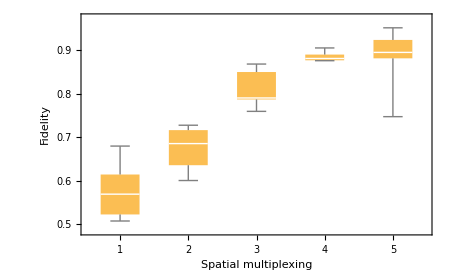

```mathematica
BoxWhiskerChart[listresultsspat,ChartLabels->listm,FrameLabel->{"Spatial multiplexing","Fidelity"},ImageSize->450,LabelStyle->15]
```

## 2.3 Temporal multiplexing

### Seed for RNG

```mathematica
seed=401;
```

### Other parameters

```mathematica
listtemp=Range[5];
```

#### Channel and task

```mathematica
nchan=2;
{gchan,ωbarechan}={0.1,0.25};
Δtchan=1.5Pi ωbarechan^-1;
ρlimitchan=0.95;
delay=0;
temp=1;
```

#### Reservoir

```mathematica
n=3;
{g,ωbare}={0.1,ωbarechan};(*every bare frequency is assumed to be the same*)
Δt=Δtchan;(*processing speed is dictated by the channel*)
ρlimit=0.99;
```

#### Input

```mathematica
m=1;
{prep,train,test}={40,80,40};
{nthmax,rmax}={10.,1.};
```

### More computations: vary m for some realizations

#### Reset RNG

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

#### Do it

```mathematica
listresultstemp=ParallelTable[
(*random reservoir, random task*)
{matH,initσ}=getrandomreservoir[n,ωbare,g];
{getinput,gettarget,figureofmerit}=makeQChan[ωbare,m,temp];
listinput=getinput[nthmax,rmax,prep,train,test];
listtarget=gettarget[listinput,delay];
trainingfunction=getQChantrainingfunction[matH,initσ,m,nchan,gchan,ωbare,Δt,ρlimitchan,temp];
(*bona fide initial points*)
initpoints=3 10n m;
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
(*train and test*)
First@trainertester[trainingfunction,figureofmerit,listinput,listtarget,prep,train,test,method,n,g],
{realizations},{temp,listtemp},Method->"FinestGrained"]ᵀ;//AbsoluteTiming
```

{1194.72,Null}

```mathematica
listresultstemp=Developer`ToPackedArray[listresultstemp];
```

### Show results

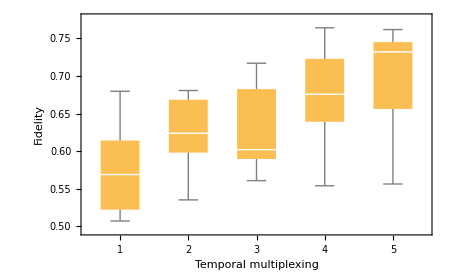

```mathematica
BoxWhiskerChart[listresultstemp,ChartLabels->listtemp,FrameLabel->{"Temporal multiplexing","Fidelity"},ImageSize->450,LabelStyle->15]
```

## 2.4. Both multiplexings

### Seed for RNG

```mathematica
seed=402;
```

### Other parameters

```mathematica
listtemp=Range[2,4];
listspat=Range[2,4];
```

#### Channel and task

```mathematica
nchan=2;
{gchan,ωbarechan}={0.1,0.25};
Δtchan=1.5Pi ωbarechan^-1;
ρlimitchan=0.95;
delay=0;
temp=1;
```

#### Reservoir

```mathematica
n=3;
{g,ωbare}={0.1,ωbarechan};(*every bare frequency is assumed to be the same*)
Δt=Δtchan;(*processing speed is dictated by the channel*)
ρlimit=0.99;
```

#### Input

```mathematica
m=1;
{prep,train,test}={40,80,40};
{nthmax,rmax}={10.,1.};
```

### More computations: vary m for some realizations

#### Reset RNG

```mathematica
SeedRandom[seed];
listparallelseeds=RandomInteger[{-1000,1000},$KernelCount];
Do[(*seed each subkernel with its own seed*)
ParallelEvaluate[SeedRandom[listparallelseeds[[ker]]],Kernels[][[ker]]],
{ker,$KernelCount}
];
```

#### Do it

```mathematica
listresultsboth2=ParallelTable[
(*random reservoir, random task*)
{matH,initσ}=getrandomreservoir[n,ωbare,g];
{getinput,gettarget,figureofmerit}=makeQChan[ωbare,m,temp];
listinput=getinput[nthmax,rmax,prep,train,test];
listtarget=gettarget[listinput,delay];
trainingfunction=getQChantrainingfunction[matH,initσ,m,nchan,gchan,ωbare,Δt,ρlimitchan,temp];
(*bona fide initial points*)
initpoints=3 10n m;
listinitpoints=getinitpoints[matH,m,ωbare,Δt,initpoints,g,ρlimit];
method={"DifferentialEvolution","ScalingFactor"->0.05,"CrossProbability"->0.4,"InitialPoints"->listinitpoints};
(*train and test*)
First@trainertester[trainingfunction,figureofmerit,listinput,listtarget,prep,train,test,method,n,g],
{realizations},{temp,listtemp},{m,listspat},Method->"FinestGrained"]ᵀ;//AbsoluteTiming
```

{7848.43,Null}

```mathematica
listresultsboth2=Developer`ToPackedArray[listresultsboth2];
```

### Show results

```mathematica
(listresultsboth=Transpose[listresultsboth2ᵀ,{3,1,2}])//Dimensions
```

{3,3,6}

```mathematica
listmedianresults=Map[Median,listresultsboth,{2}];
```

```mathematica
listmedianresults//MatrixForm
```

(0.751742 | 0.834862 | 0.887023
0.838385 | 0.861558 | 0.889002
0.77752 | 0.871537 | 0.770094)

```mathematica
(*cases where one is kept at order 1 have already been computed elsewhere*)
(listmedianresultsfull=Join[{Map[Median,listresultstemp[[;;4]]]}ᵀ,Join[{Map[Median,listresultsspat[[2;;4]]]},listmedianresults],2])//MatrixForm
```

(0.568837 | 0.68536 | 0.790496 | 0.881481
0.623741 | 0.751742 | 0.834862 | 0.887023
0.601942 | 0.838385 | 0.861558 | 0.889002
0.675681 | 0.77752 | 0.871537 | 0.770094)

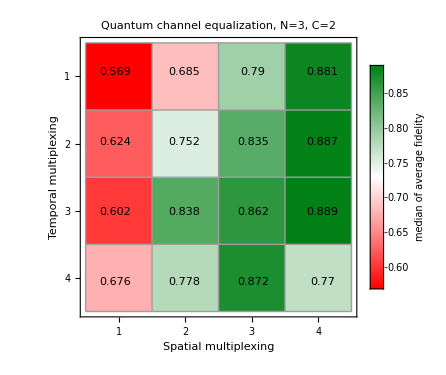

```mathematica
plotmedianresults=ArrayPlot[listmedianresultsfull,ImageSize->375,LabelStyle->15,PlotLegends->BarLegend[Automatic,Automatic,LegendLabel->Placed[Rotate["median of average fidelity",1.5Pi],Right]],FrameLabel->{"Temporal multiplexing","Spatial multiplexing"},ColorFunctionScaling->True,ColorFunction->"RedGreenSplit",PlotLabel->"Quantum channel equalization, N=3, C=2",FrameTicks->{{True,False},{True,False}},Mesh->True,Frame->True,makearraylabels[listmedianresultsfull,0.001,Directive[Black,Medium]]]
```

## 2.5 Figure 3

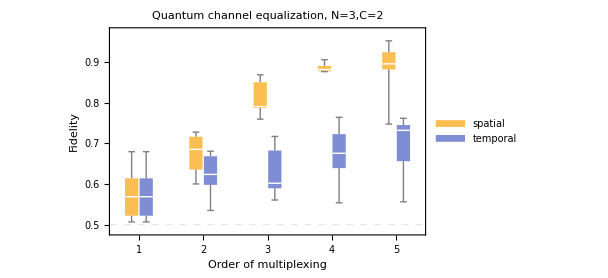

```mathematica
plotboth=BoxWhiskerChart[{listresultsspat,listresultstemp}ᵀ,ChartLabels->{Range[5],None},FrameLabel->{"Order of multiplexing","Fidelity"},ImageSize->450,LabelStyle->15,GridLines->{None, {0.5}},GridLinesStyle->Directive[Dashed,Thick],ChartLegends->Placed[{"spatial","temporal"},Scaled[{0.15,0.85}]],PlotLabel->"Quantum channel equalization, N=3,C=2",BarSpacing->{0.1,2.5}]
```

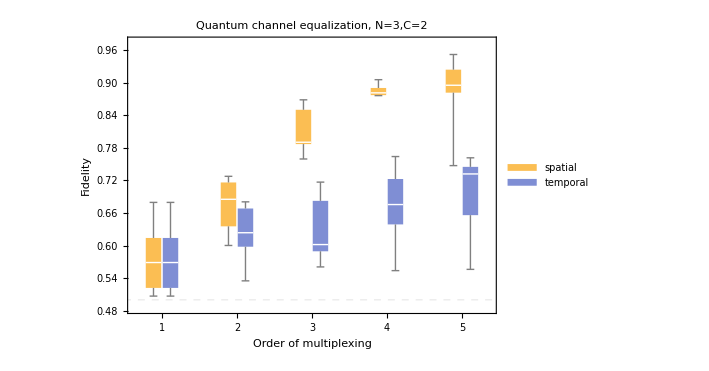
a |  | b
-Graphics- |  | -Graphics-

```mathematica
s=Spacer[30];
plotcombo=Grid[
{{Style["a",20,Bold],"",Style["b",20,Bold]},{Show[plotboth,ImageSize->525,AspectRatio->1./Sqrt[2],ImagePadding->{{Automatic, 5}, {Automatic, 9}}],s,Show[plotmedianresults,ImagePadding->{{Automatic, 5}, {Automatic, 11}}]}},Alignment->Left
]
```